# DYS HW4-1

-Graphics-

## a.) Fixed points of Lorentz System -Graphics-

```mathematica
ClearAll["Global`*"]

xPrime = s * y - s * x;
yPrime = r * x - y - x * z;
zPrime = x * y - b * z;

s = 10;
b = 8/3;
r = 28;

FP1 = {0,0,0};
FP2 = {Sqrt[72],Sqrt[72],27};
FP3 = {-Sqrt[72],-Sqrt[72],27};


Jacobi = D[{xPrime,yPrime,zPrime},{{x,y,z}}]
JacobMatrix = Jacobi // MatrixForm
Eig = N[Eigenvalues[Jacobi]]

(*Parameters*)
s = 10;
b = 8/3;
r = 28;
x = 0;
y = 0;
z = 0;
Eig = N[Eigenvalues[Jacobi]]

x = Sqrt[72];
y = Sqrt[72];
z = 27;
Eig = N[Eigenvalues[Jacobi]]

x = -Sqrt[72];
y = -Sqrt[72];
z = 27;
Eig = N[Eigenvalues[Jacobi]]
```

{{-10,10,0},{28-z,-1,-x},{y,x,-8/3}}

(-10 | 10 | 0
28-z | -1 | -x
y | x | -8/3)

{0.333333 Root[-19440+270 x^2+270 x y+720 z+(-2166+9 x^2+90 z) #1+41 #1^2+#1^3&,1],0.333333 Root[-19440+270 x^2+270 x y+720 z+(-2166+9 x^2+90 z) #1+41 #1^2+#1^3&,2],0.333333 Root[-19440+270 x^2+270 x y+720 z+(-2166+9 x^2+90 z) #1+41 #1^2+#1^3&,3]}

{-22.8277,11.8277,-2.66667}

{-13.8546,0.0939556+10.1945 ⅈ,0.0939556-10.1945 ⅈ}

{-13.8546,0.0939556+10.1945 ⅈ,0.0939556-10.1945 ⅈ}

for FP1 = {-22.8277,11.8277,-2.66667}, for FP2 = {-13.8546,0.0939556+10.1945 ⅈ,0.0939556-10.1945 ⅈ}, for FP3 = {-13.8546,0.0939556+10.1945 ⅈ,0.0939556-10.1945 ⅈ}

## b.) Solve system numerically

-Graphics-

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…],z→InterpolatingFunction[…]}}

-Graphics3D-

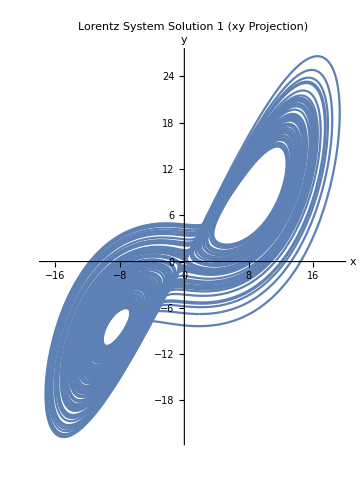

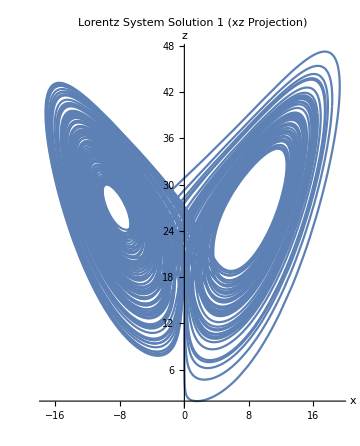

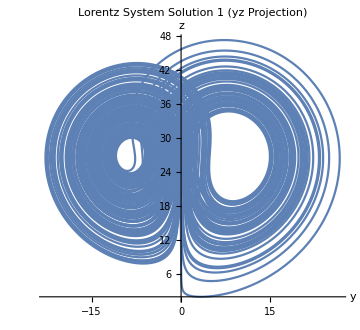

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
ClearAll["Global`*"]

(*Parameters of Lorentz*)
s = 10;
b = 8/3;
r = 28;

xPrime = s * y - s * x;
yPrime = r * x - y - x * z;
zPrime = x * y - b * z;

system1 = {
	x'[t] == s * y[t] - s * x[t],
	y'[t] == r * x[t] - y[t] - x[t] * z[t],
	z'[t] == x[t] * y[t] - b * z[t]
};
 
FP1 = {0,0,0};
delta = 0.1;
startingPoint1 = FP1 + delta;

initialConditions1 = {x[0] == startingPoint1[[1]], y[0] == startingPoint1[[2]], z[0] == startingPoint1[[3]]};


t0 = 0;
tMax = 100;
tIntersting = 10;

solution1 = NDSolve[{system1, initialConditions1}, {x,y,z}, {t, t0, tMax}]

(* Define the solution function *)
sol1[t_] = {x[t], y[t], z[t]} /. solution1[[1]];

(* Plot the solution using ParametricPlot3D *)
ParametricPlot3D[sol1[t], {t, tIntersting, tMax}, PlotRange -> All, AxesLabel -> {"x", "y", "z"}, 
  PlotLabel -> "Lorentz System Solution 1", ImageSize -> Large, MaxRecursion -> 15]

(* Define the solution functions for each variable *)
xSol[t_] = x[t] /. solution1[[1]];
ySol[t_] = y[t] /. solution1[[1]];
zSol[t_] = z[t] /. solution1[[1]];

(* Plot xy, xz, and yz projections *)
xyPlot = ParametricPlot[{xSol[t], ySol[t]}, {t, tIntersting, tMax}, 
  PlotRange -> All, AxesLabel -> {"x", "y"}, MaxRecursion -> 15,
  PlotLabel -> "Lorentz System Solution 1 (xy Projection)", ImageSize -> Medium];

xzPlot = ParametricPlot[{xSol[t], zSol[t]}, {t, tIntersting, tMax}, 
  PlotRange -> All, AxesLabel -> {"x", "z"},MaxRecursion -> 15, 
  PlotLabel -> "Lorentz System Solution 1 (xz Projection)", ImageSize -> Medium];

yzPlot = ParametricPlot[{ySol[t], zSol[t]}, {t, tIntersting, tMax}, 
  PlotRange -> All, AxesLabel -> {"y", "z"}, MaxRecursion -> 15,
  PlotLabel -> "Lorentz System Solution 1 (yz Projection)", ImageSize -> Medium];

(* Show all plots *)
Show[xyPlot]
Show[xzPlot]
Show[yzPlot]
(*
```

## c.) Compute the stability matrix J

```mathematica
(* Analog a.) *)
```

## d.) Trace of the stability matrix and sum of the Lyapunov Exponents

```mathematica
ClearAll["Global`*"]

xPrime = s * y - s * x;
yPrime = r * x - y - x * z;
zPrime = x * y - b * z;

(*s = 10;
b = 8/3;
r = 28;*)

FP1 = {0,0,0};
FP2 = {Sqrt[72],Sqrt[72],27};
FP3 = {-Sqrt[72],-Sqrt[72],27};

Jacobi = D[{xPrime,yPrime,zPrime},{{x,y,z}}]

traceJ = Tr[Jacobi]
eigVl = Eigenvalues[Jacobi];
sumOfEigVl = Total[eigVl] // Simplify
```

{{-s,s,0},{r-z,-1,-x},{y,x,-b}}

-1-b-s

-1-b-s